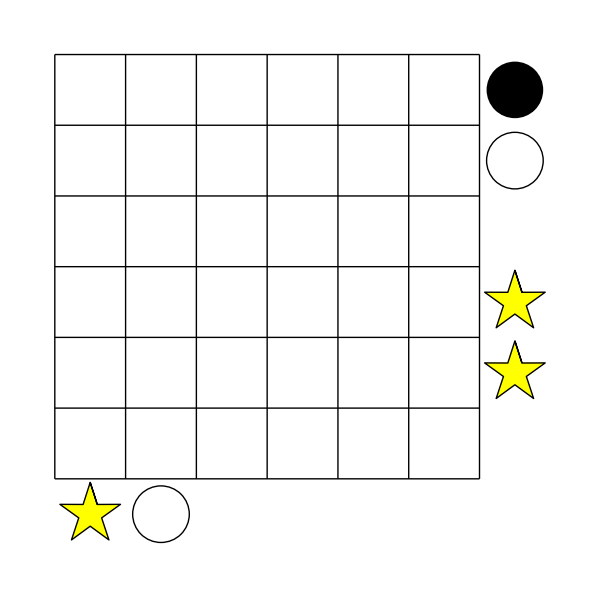
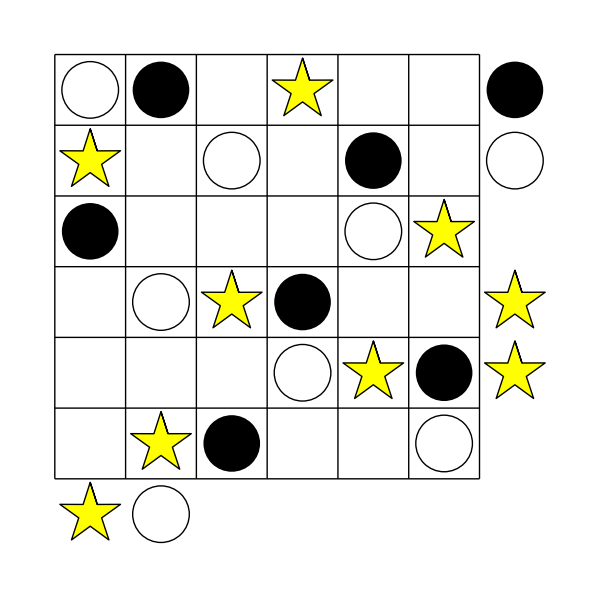

-Graphics-  -Graphics-

```mathematica
alldiff[L_]:=Length[L]==Length[Union[L]]
```

```mathematica
c[1,x_,y_]:=Circle[{x-.5,y-.5},.4]
```

```mathematica
c[2,x_,y_]:=Disk[{x-.5,y-.5},.4]
```

```mathematica
pt[t_]:={Cos[2Pi t/5],Sin[2Pi t/5]}
```

```mathematica
c[3,x_,y_]:={Yellow,Polygon[Flatten[Transpose[{Table[{x-.5,y-.5}+.18pt[i-1/4],{i,1,5}],Table[{x-.5,y-.5}+.45pt[i+1/4],{i,1,5}]},{2,1,3}],1]],Black,Line[Flatten[Transpose[{Table[{x-.5,y-.5}+.17pt[i-1/4],{i,1,6}],Table[{x-.5,y-.5}+.45pt[i+1/4],{i,1,6}]},{2,1,3}],1]]}
```

```mathematica
pic[L_]:=Graphics[{
MapIndexed[c[1,#1,#2[[1]]]&,L[[1]]],MapIndexed[c[2,#1,#2[[1]]]&,L[[2]]],MapIndexed[c[3,#1,#2[[1]]]&,L[[3]]],Black,
Style[{Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}]},Antialiasing->False]
},ImageSize->20n]
```

```mathematica
beforepic[L_,sides_]:=Graphics[{
Style[{Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}]},Antialiasing->False],
Map[If[#>n,c[spectrum[L][[#]],n+1,#-n],c[spectrum[L][[#]],#,0]]&,sides]
},ImageSize->20(n+1)]
```

```mathematica
pic[L_,sides_]:=Graphics[{
MapIndexed[c[1,#1,#2[[1]]]&,L[[1]]],MapIndexed[c[2,#1,#2[[1]]]&,L[[2]]],MapIndexed[c[3,#1,#2[[1]]]&,L[[3]]],Black,
Style[{Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}]},Antialiasing->False],
Map[If[#>n,c[spectrum[L][[#]],n+1,#-n],c[spectrum[L][[#]],#,0]]&,sides]
},ImageSize->20(n+1)]
```

```mathematica
sight[{white_,black_,stars_}]:=(dw=Abs[white-stars];db=Abs[black-stars];Which[dw>db,2,dw<db,1,True,3])
```

```mathematica
ccc[L_]:=Table[Position[L,i][[1,1]],{i,1,n}]
```

```mathematica
spectrum[L_]:=Map[sight,Transpose[Map[ccc,L]],1]~Join~Map[sight,Transpose[L],1]
```

```mathematica
ran:=RandomInteger[{1,2n}];
```

```mathematica
ranc:=RandomInteger[{1,3}];
```

```mathematica
n=5;
```

```mathematica
p=Select[Permutations[Range[n]],Min[Abs[Rest[#-RotateRight[#]]]]>1&];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,p,1],2],Apply[And,Map[alldiff,Transpose[#]]]&];
```

```mathematica
For[i=1,i≤n-1,i++,
For[j=i+1,j≤n+1-i,j++,
For[k=n+1,k≤3n/2,k++,
For[ci=1,ci≤3,ci++,
For[cj=1,cj≤3,cj++,
For[ck=1,ck≤3,ck++,
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k}],"  ",pic[poss[[1]],{i,j,k}]]]]]]]]]
```

```mathematica
n=6;
```

```mathematica
p=Select[Permutations[Range[n]],Min[Abs[Rest[#-RotateRight[#]]]]>1&];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,p,1],2],Apply[And,Map[alldiff,Transpose[#]]]&];
```

```mathematica
Length[s]
```

47664

```mathematica
ss=Select[s,Max[spectrum[#]]<3&];
```

```mathematica
f[list_,clist_]:=Select[s,Apply[And,Table[spectrum[#][[list[[ii]]]]==clist[[ii]],{ii,1,Length[list]}]]&]
```

```mathematica
For[ct=1,ct>0,ct++,
numstar=RandomInteger[{1,4}];
list=Table[RandomInteger[{1,2n}],{9-numstar}];
While[Length[Union[list]]<Length[list],list=Table[RandomInteger[{1,2n}],{9-numstar}]];
clist=Table[3,{numstar}]~Join~Table[RandomInteger[{1,2}],{9-2numstar}];
poss=f[list,clist];If[Length[poss]==1,Print[beforepic[poss[[1]],list],"  ",pic[poss[[1]],list]]]]
```

$Aborted

## 5x5

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«9 more identical outputs»

## 6x6 - 4 stars

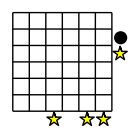
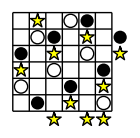

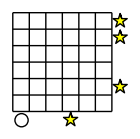
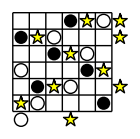

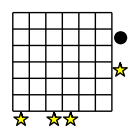
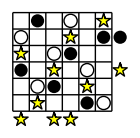

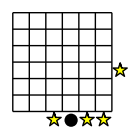
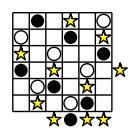

## 6x6 - 3 stars

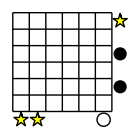
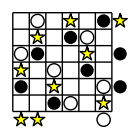

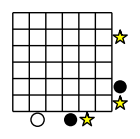
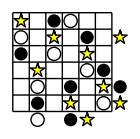

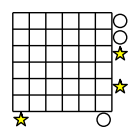
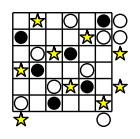

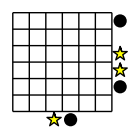
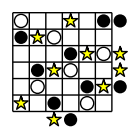

## 6x6 - 2 stars

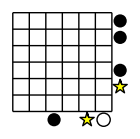
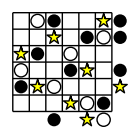

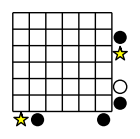
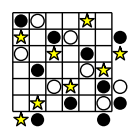

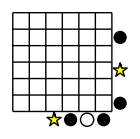
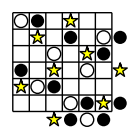

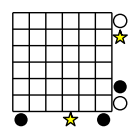
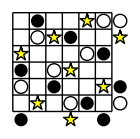

## 6x6 - 1 star

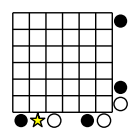
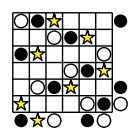

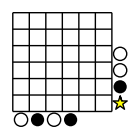
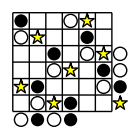

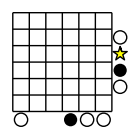
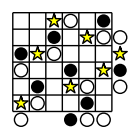

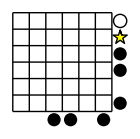
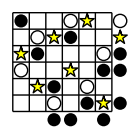

## 6x6 - 0 stars